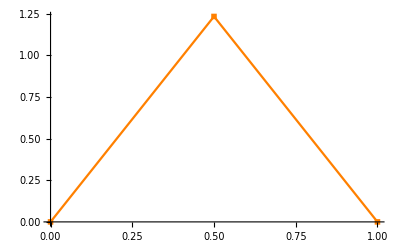

```mathematica
G1=ListPlot[{{0,0},{0.5,1.23370055},{1,0}},Joined->True,PlotStyle->Orange,PlotMarkers->{■,20}]
```

```mathematica
▲
```

```mathematica
U[[1]]={1.23370055}
```

{1.2337}

```mathematica
●
```

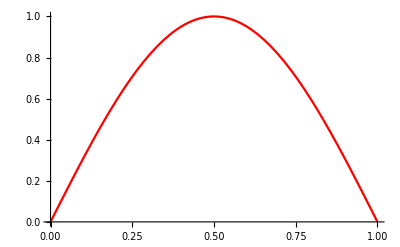

```mathematica
H2=Plot[Sin[Pi*x],{x,0,1},PlotStyle->Red]
```

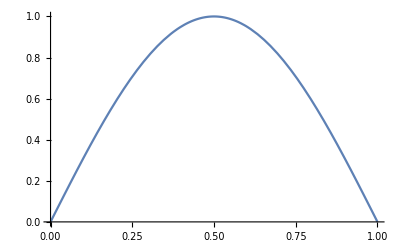

```mathematica
Show[G2,PlotStyle->Green]
```

```mathematica
Rasterize[G2,"Image"]
```

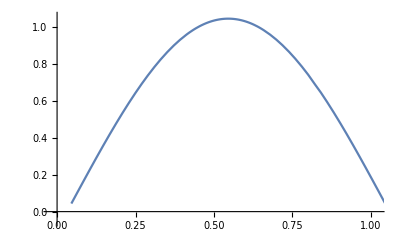

```mathematica
U[[2]]={0.74460415,1.05302929,0.74460415}
```

{0.744604,1.05303,0.744604}

```mathematica
n=4
```

4

```mathematica
For[i=1,i<n,i++,Print[{i*1/(n),U[[i]]}]]
```

{1/4,0.744604}

{1/2,1.05303}

{3/4,0.744604}

```mathematica
m={1,2,3,4}
```

{1,2,3,4}

```mathematica
m[[1]]
```

1

```mathematica
U[[1]]
```

Part::partd: Part specification U⟦1⟧ is longer than depth of object.

U⟦1⟧

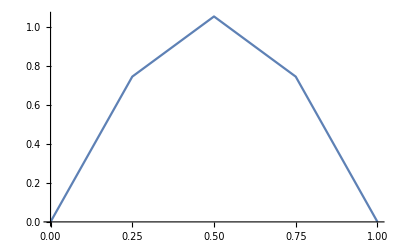

```mathematica
G3=ListPlot[{{0,0},{1/4,0.74460415},{1/2,1.05302929},{3/4,0.74460415},{1,0}},Joined->True]
```

```mathematica
Interpolation[{{1/4,0.74460415},{1/2,1.05302929},{3/4,0.74460415}}]
```

Interpolation::inhr: Requested order is too high; order has been reduced to {2}.

InterpolatingFunction[…]

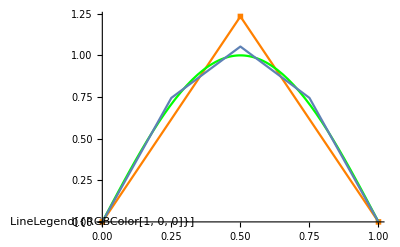

```mathematica
Show[{G1,G2,G3},Epilog->Inset[Framed[Column[{PointLegend[{Blue},{"    Data"}],LineLegend[{Red}]}]]]]
```

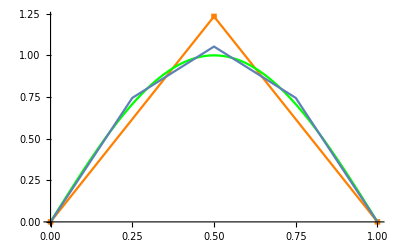

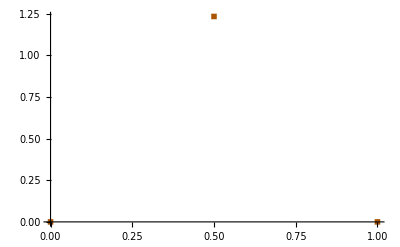

```mathematica
G4=ListPlot[{{0,0},{0.5,1.23370055},{1,0}},PlotMarkers->{■,100},PlotStyle->Darker[Orange]]
```

```mathematica
PlotS
```

```mathematica
Manipulate[ListPlot[{{0,0},{0.5,1.23370055},{1,0}},PlotMarkers->"■",PlotStyle->RGBColor[r,g,b]],{r,0,1,Appearance->"Labeled"},{g,0,1,Appearance->"Labeled"},{b,0,1,Appearance->"Labeled"},SaveDefinitions->True]
```

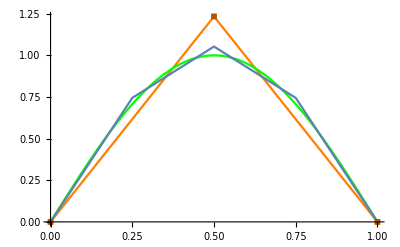

```mathematica
Show[{G1,G2,G3,G4}]
```

```mathematica
U[[3]]={0.38763947,0.71626434,0.93584446,1.01295075,0.93584446,0.71626434,0.38763947}
```

{0.387639,0.716264,0.935844,1.01295,0.935844,0.716264,0.387639}

```mathematica
For[i=1,i<8,i++,Print[{i*1/(8),U1[[i]]}]]
```

{1/8,0.387639}

{1/4,0.716264}

{3/8,0.935844}

{1/2,1.01295}

{5/8,0.935844}

{3/4,0.716264}

{7/8,0.387639}

```mathematica
PrintingOptions
```

```mathematica
U8=Table[{i*1/8,U1[[i]]},{i,1,7}]
```

{{1/8,0.387639},{1/4,0.716264},{3/8,0.935844},{1/2,1.01295},{5/8,0.935844},{3/4,0.716264},{7/8,0.387639}}

```mathematica
{{1/8,0.38763947},{1/4,0.71626434},{3/8,0.93584446},{1/2,1.01295075},{5/8,0.93584446},{3/4,0.71626434},{7/8,0.38763947}}
```

{{1/8,0.387639},{1/4,0.716264},{3/8,0.935844},{1/2,1.01295},{5/8,0.935844},{3/4,0.716264},{7/8,0.387639}}

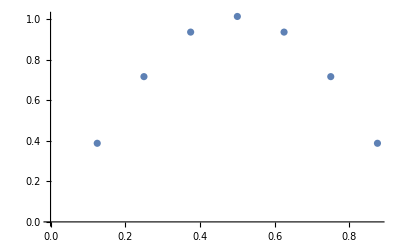

```mathematica
ListPlot[U8]
```

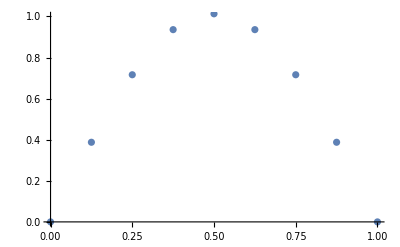

```mathematica
Show[ListPlot[U8],ListPlot[{{0,0},{1,0}}],PlotRange->{0,1}]
```

```mathematica
U[[1]]={1,2,3}
```

{1,2,3}

```mathematica
U[[1]]
```

{1,2,3}

```mathematica
U[[1,2]]
```

2

```mathematica
For[n=2,n≤8,n=n*2,
ListPlot[Table[{k*1/(n),U[[Log[2,n],k]]},{k,1,n-1}]]

]
```

{{1/2,1.2337}}

{{1/4,0.744604},{1/2,1.05303},{3/4,0.744604}}

{{1/8,0.387639},{1/4,0.716264},{3/8,0.935844},{1/2,1.01295},{5/8,0.935844},{3/4,0.716264},{7/8,0.387639}}

```mathematica
Log[2,8]
```

3

```mathematica
U[[2]]
```

{0.744604,1.05303,0.744604}

```mathematica
For[i=0,i≤2,i++,
ListPlot[Table[{k*1/(4),U[[Log[2,4],k]]},{k,1,3}]]
]
```

```mathematica
Log[2,4]
```

2

```mathematica
ListPlot[Table[{k*1/(4),U[[Log[2,4],k]]},{k,1,3}]]
```

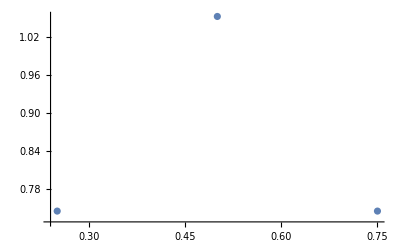
```mathematica
-Graphics-
n=2
```

-Graphics-

2

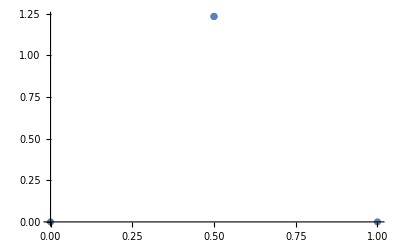
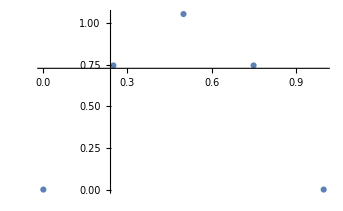
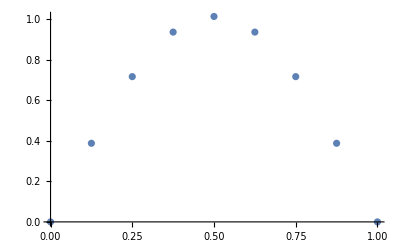

```mathematica
Table[Show[ListPlot[Table[{k*1/(n),U[[Log[2,n],k]]},{k,1,n-1}]],ListPlot[{{0,0},{1,0}}],PlotRange->Automatic],{n,{2,4,8}}]
```

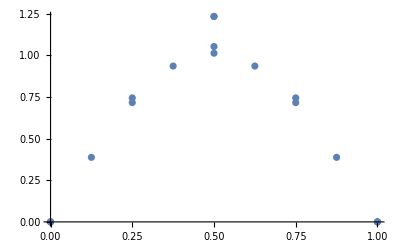

```mathematica
Show[Table[Show[ListPlot[Table[{k*1/(n),U[[Log[2,n],k]]},{k,1,n-1}]],ListPlot[{{0,0},{1,0}}],PlotRange->Automatic],{n,{2,4,8}}]]
```

```mathematica
Show[Table[Show[ListPlot[Table[{k*1/(n),U[[Log[2,n],k]]},{k,1,n-1}]],ListPlot[{{0,0},{1,0}}],PlotRange->Automatic],{n,{2,4,8}}]]
```

-Graphics-

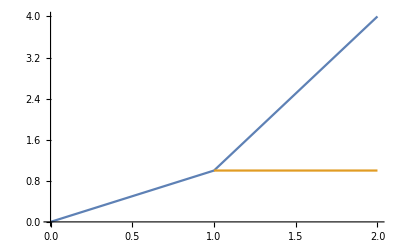

```mathematica
ListPlot[{Table[{i,i^2},{i,0,2}],{{2,1},{1,1}}},Joined->True]
```

```mathematica
Insert[Table[{i,i^2},{i,0,2}],{{3,1},{7,7}},{1,3}]
```

{{0,0,{{3,1},{7,7}}},{1,1},{2,4}}

```mathematica
Insert[{{0,0},{1,1},{2,4}},{1,3}]
```

Insert[{{0,0},{1,1},{2,4}},{1,3}]

```mathematica
-
```

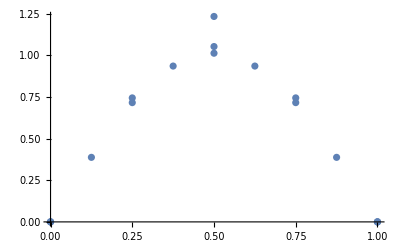

```mathematica
Show[Table[ListPlot[Insert[Insert[Table[{k*1/(n),U[[Log[2,n],k]]},{k,1,n-1}],{0,0},1],{1,0},1]],{n,{2,4,8}}]]
```

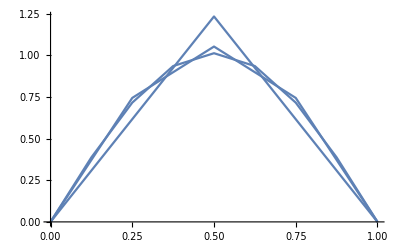

```mathematica
Show[Table[ListPlot[Insert[Insert[Table[{k*1/(n),U[[Log[2,n],k]]},{k,1,n-1}],{0,0},1],{1,0},n+1],Joined->True],{n,{2,4,8}}]]
```

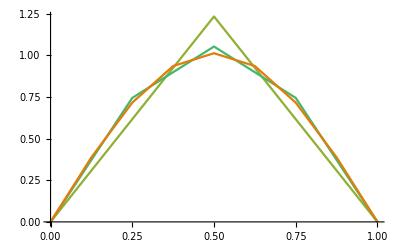

```mathematica
Show[Table[ListPlot[Insert[Insert[Table[{k*1/(n),U[[Log[2,n],k]]},{k,1,n-1}],{0,0},1],{1,0},n+1],Joined->True,PlotStyle->ColorData[97,n^2-1]],{n,{2,4,8}}]]
```

```mathematica
ColorData[]
```

{Gradients,Indexed,Named,Physical}

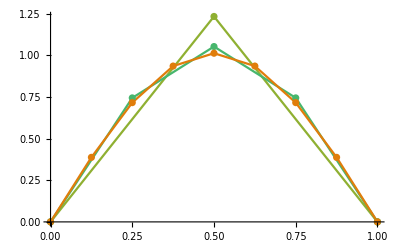

```mathematica
Show[Table[ListPlot[Insert[Insert[Table[{k*1/(n),U[[Log[2,n],k]]},{k,1,n-1}],{0,0},1],{1,0},n+1],Joined->True,PlotStyle->ColorData[97,n^2-1]],{n,{2,4,8}}],Table[ListPlot[Insert[Insert[Table[{k*1/(n),U[[Log[2,n],k]]},{k,1,n-1}],{0,0},1],{1,0},n+1],PlotStyle->ColorData[97,n^2-1]],{n,{2,4,8}}]]
```

```mathematica
U[[4]]={0.19571831,0.38391528,0.55735859,0.70938293,0.83414608,0.92685347,0.98394239,1.00321896,0.98394239,0.92685347,0.83414608,0.70938293,0.55735859,0.38391528,0.19571831}
```

Set::partw: Part 4 of {{1.2337},{0.744604,1.05303,0.744604},{0.387639,0.716264,0.935844,1.01295,0.935844,0.716264,0.387639}} does not exist.

{0.195718,0.383915,0.557359,0.709383,0.834146,0.926853,0.983942,1.00322,0.983942,0.926853,0.834146,0.709383,0.557359,0.383915,0.195718}

```mathematica
Show[Table[ListPlot[Insert[Insert[Table[{k*1/(n),U[[Log[2,n],k]]},{k,1,n-1}],{0,0},1],{1,0},n+1],Joined->True,PlotStyle->ColorData[97,n^2-1]],{n,{2,4,8}}],Table[ListPlot[Insert[Insert[Table[{k*1/(n),U[[Log[2,n],k]]},{k,1,n-1}],{0,0},1],{1,0},n+1],PlotStyle->ColorData[97,n^2-1]],{n,{2,4,8}}]]
```

-Graphics-

```mathematica
U[[5]]={1,1,1,1,1,1,1,1,1,1}
```

Set::partw: Part 5 of {{1.2337},{0.744604,1.05303,0.744604},{0.387639,0.716264,0.935844,1.01295,0.935844,0.716264,0.387639}} does not exist.

{1,1,1,1,1,1,1,1,1,1}

```mathematica
U[[4]]
```

Part::partw: Part 4 of {{1.2337},{0.744604,1.05303,0.744604},{0.387639,0.716264,0.935844,1.01295,0.935844,0.716264,0.387639}} does not exist.

{{1.2337},{0.744604,1.05303,0.744604},{0.387639,0.716264,0.935844,1.01295,0.935844,0.716264,0.387639}}⟦4⟧

```mathematica
U[[1]]
```

{1.2337}

```mathematica
U[[2]]
```

{0.744604,1.05303,0.744604}

```mathematica
U[[3]]
```

{0.387639,0.716264,0.935844,1.01295,0.935844,0.716264,0.387639}

```mathematica
U[[4]]={0.19571831,0.38391528,0.55735859,0.70938293,0.83414608,0.92685347,0.98394239,1.00321896,0.98394239,0.92685347,0.83414608,0.70938293,0.55735859,0.38391528,0.19571831}
```

Set::partw: Part 4 of {{1.2337},{0.744604,1.05303,0.744604},{0.387639,0.716264,0.935844,1.01295,0.935844,0.716264,0.387639}} does not exist.

{0.195718,0.383915,0.557359,0.709383,0.834146,0.926853,0.983942,1.00322,0.983942,0.926853,0.834146,0.709383,0.557359,0.383915,0.195718}

```mathematica
S[[1]]={1,1,1,1}
```

Set::noval: Symbol S in part assignment does not have an immediate value.

{1,1,1,1}

```mathematica
D1[[1]]={1}
```

{1}

```mathematica
D1[[2]]={1}
```

{1}

```mathematica
D1[[3]]={1}
```

{1}

```mathematica
D1[[4]]={1}
```

Set::partw: Part 4 of {{1},{1},{1}} does not exist.

{1}

```mathematica
D2={{1,2,3},{4,5,6,7,8},{9,10,11,12,13,14,15},{16,17,18,19,20,21,22,23,24,25}}
```

{{1,2,3},{4,5,6,7,8},{9,10,11,12,13,14,15},{16,17,18,19,20,21,22,23,24,25}}

```mathematica
D2[[4,2]]
```

17

```mathematica
U
```

{{1.2337},{0.744604,1.05303,0.744604},{0.387639,0.716264,0.935844,1.01295,0.935844,0.716264,0.387639}}

```mathematica
U={{1.23370055},{0.74460415,1.05302929,0.74460415},{0.38763947,0.71626434,0.93584446,1.01295075,0.93584446,0.71626434,0.38763947},{0.19571831,0.38391528,0.55735859,0.70938293,0.83414608,0.92685347,0.98394239,1.00321896,0.98394239,0.92685347,0.83414608,0.70938293,0.55735859,0.38391528,0.19571831}}
```

{{1.2337},{0.744604,1.05303,0.744604},{0.387639,0.716264,0.935844,1.01295,0.935844,0.716264,0.387639},{0.195718,0.383915,0.557359,0.709383,0.834146,0.926853,0.983942,1.00322,0.983942,0.926853,0.834146,0.709383,0.557359,0.383915,0.195718}}

```mathematica
u
```

u

```mathematica
U
```

{{1.2337},{0.744604,1.05303,0.744604},{0.387639,0.716264,0.935844,1.01295,0.935844,0.716264,0.387639},{0.195718,0.383915,0.557359,0.709383,0.834146,0.926853,0.983942,1.00322,0.983942,0.926853,0.834146,0.709383,0.557359,0.383915,0.195718}}

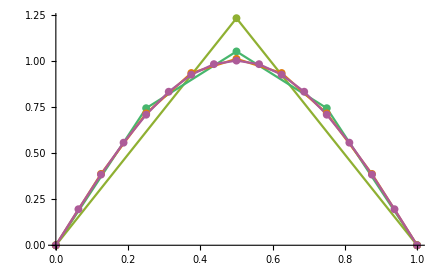

```mathematica
Show[Table[ListPlot[Insert[Insert[Table[{k*1/(n),U[[Log[2,n],k]]},{k,1,n-1}],{0,0},1],{1,0},n+1],Joined->True,PlotStyle->ColorData[97,n^2-1]],{n,{2,4,8,16}}],Table[ListPlot[Insert[Insert[Table[{k*1/(n),U[[Log[2,n],k]]},{k,1,n-1}],{0,0},1],{1,0},n+1],PlotStyle->ColorData[97,n^2-1]],{n,{2,4,8,16}}]]
```

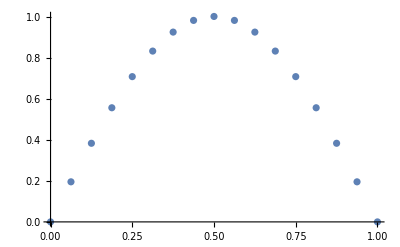

```mathematica
ListPlot[Insert[Insert[Table[{k*1/(16),U[[4,k]]},{k,1,15}],{0,0},1],{1,0},17]]
```

```mathematica
U[[4]]
```

{0.195718,0.383915,0.557359,0.709383,0.834146,0.926853,0.983942,1.00322,0.983942,0.926853,0.834146,0.709383,0.557359,0.383915,0.195718}

```mathematica
Insert[U[[4]],{0,0},1]
```

{{0,0},0.195718,0.383915,0.557359,0.709383,0.834146,0.926853,0.983942,1.00322,0.983942,0.926853,0.834146,0.709383,0.557359,0.383915,0.195718}

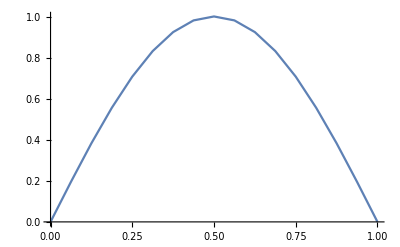

```mathematica
ListPlot[Insert[Insert[Table[{k*1/(16),U[[4,k]]},{k,1,15}],{0,0},1],{1,0},17],Joined->True]
```

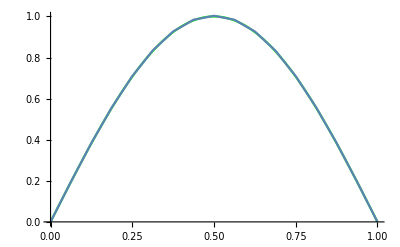

```mathematica
Show[G2,ListPlot[Insert[Insert[Table[{k*1/(16),U[[4,k]]},{k,1,15}],{0,0},1],{1,0},17],Joined->True]]
```

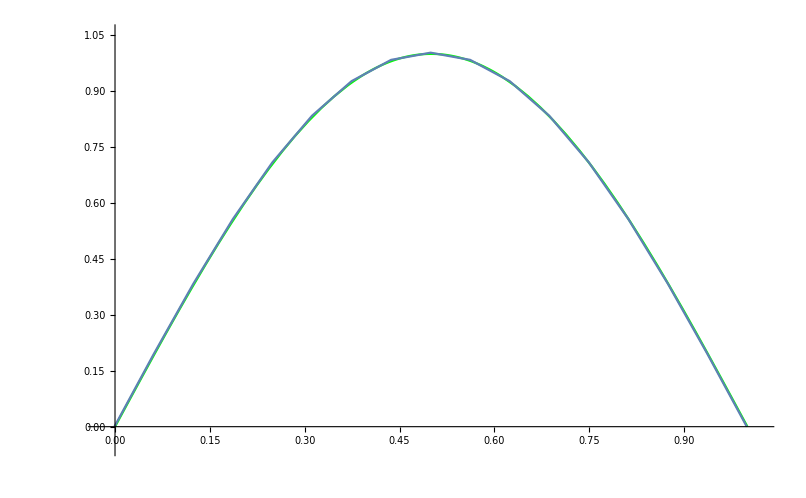

-Graphics-

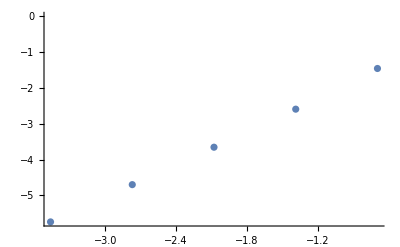

```mathematica
ListPlot[{{Log[1/2],Log[0.233700550136169]},{Log[1/4],Log[0.0749947376498495]},{Log[1/8],Log[0.0259014934437588]},{Log[1/16],Log[0.00910460633591457]},{Log[1/32],Log[0.00321431071747838]}}]
```

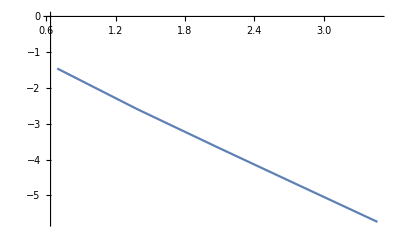

```mathematica
ListPlot[{{Log[2],Log[0.233700550136169]},{Log[4],Log[0.0749947376498495]},{Log[8],Log[0.0259014934437588]},{Log[16],Log[0.00910460633591457]},{Log[32],Log[0.00321431071747838]}},Joined->True]
```

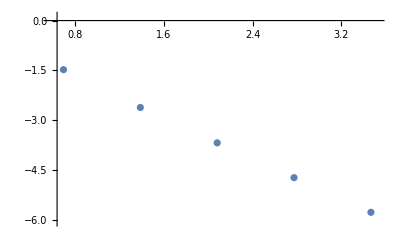

```mathematica
(Log[1/32*0.00321431071747838]-Log[1/16*0.00910460633591457])/(Log[1/32]-Log[1/16])
```

2.50209

```mathematica
0.11833817004152695*1/2
```

0.0591691

```mathematica
0.053060475247630294
```

0.0530605

```mathematica
0.053060475247630294*1/5
```

0.0106121

```mathematica
0.053060475247630294*1/4
```

0.0132651

```mathematica
(-0.01972513)^2
```

0.000389081

```mathematica
(-0.03191593)^2
```

0.00101863

```mathematica
(-0.03191593)^2
```

0.00101863

```mathematica
(-0.01972513)^2
```

0.000389081

```mathematica
0.0003890807535169+0.0010186265877649+0.0010186265877649+0.0003890807535169
```

0.00281541

```mathematica
Sqrt[0.0028154146825636]
```

0.0530605

```mathematica
(1/5)*0.0003890807535169+(1/5)*0.0010186265877649+(1/5)*0.0010186265877649+(1/5)*0.0003890807535169
```

0.000563083

```mathematica
Sqrt[0.00056308293651272]
```

0.0237294

```mathematica
0.031915926534603956*1/10
```

0.00319159

```mathematica
(Log[0.00053428]-Log[0.0020158])/(Log[1/33]-Log[1/17])
```

2.0019

```mathematica
{{m, □, □, □, □}, {□, □, □, □, □}, {□, □, □, □, □}, {□, □, □, □, □}, {□, □, □, □, □}, {□, □, □, □, □}, {□, □, □, □, □}}
```

```mathematica
(Log[0.06832257432888329]-Log[0.16525124376831238])/(Log[1/3]-Log[1/2])
```

2.17831

```mathematica
NumberForm[2.1783052558628357,16]
```

2.178305255862836

```mathematica
(Log[0.06832257432888329/0.16525124376831238])/(Log[1/3(1/2)^-1])
```

2.17831

```mathematica
(Log[0.02372936591442926/0.03749736882492478])/(Log[1/5(1/4)^-1])
```

2.05051

```mathematica
NumberForm[2.050507011751666,16]
```

2.050507011751666

```mathematica
(Log[0.00722385630996764/0.009157560828470393])/(Log[1/9(1/8)^-1])
```

2.0138

```mathematica
NumberForm[2.0137953783622486,16]
```

2.013795378362249

```mathematica
(Log[0.002015800774571253/0.002276151583978644])/(Log[1/17(1/16)^-1])
```

2.00363

```mathematica
NumberForm[2.0036346333113895,16]
```

2.00363463331139

```mathematica
(Log[0.0005342843441122418/00.00056821522629239])/(Log[1/33(1/32)^-1])
```

2.00094

```mathematica
NumberForm[2.000935025659962,16]
```

2.000935025659962

```mathematica
(Log[0.00013766626048977056/0.00014200246344626085])/(Log[1/65(1/64)^-1])
```

2.00024

```mathematica
NumberForm[2.0002372740342875,16]
```

2.000237274034288

```mathematica
(Log[0.00003494917754770403/0.00003549740806235027])/(Log[1/129(1/128)^-1])
```

2.00006

```mathematica
NumberForm[2.000059682188371,16]
```

2.000059682188371

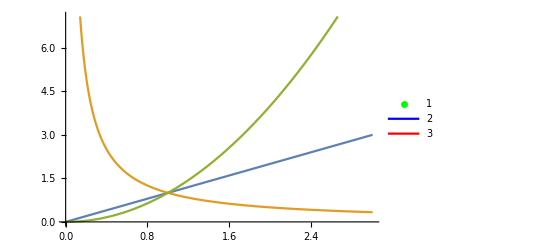

```mathematica
Plot[{x,1/x,x^2},{x,0,3},PlotLegends->(Placed[#,Right]&/@{PointLegend[{Green},{"1"}],LineLegend[{Blue,Red},{"2","3"}]})]
```

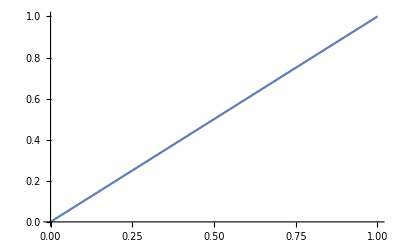

```mathematica
G1=Plot[x,{x,0,1}]
```

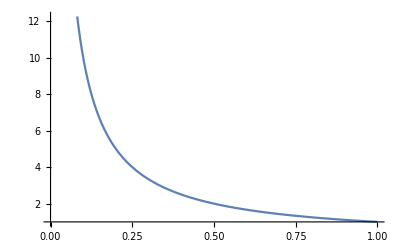

```mathematica
G2=Plot[1/x,{x,0,1}]
```

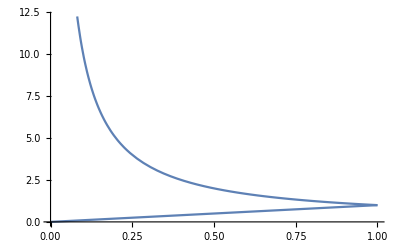

```mathematica
Show[G1,G2,PlotRange->Automatic,PlotLegends->Automatic]
```

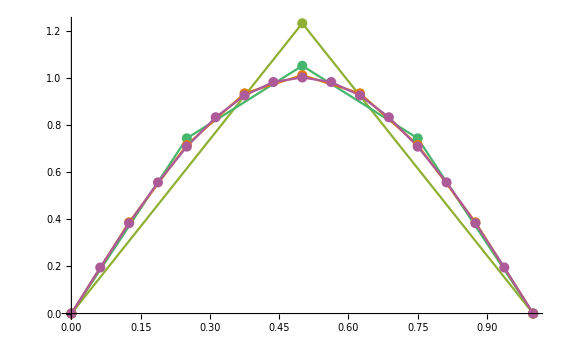

```mathematica
Show[Table[ListPlot[Insert[Insert[Table[{k*1/(n),U[[Log[2,n],k]]},{k,1,n-1}],{0,0},1],{1,0},n+1],Joined->True,PlotStyle->ColorData[97,n^2-1]],{n,{2,4,8,16}}],Table[ListPlot[Insert[Insert[Table[{k*1/(n),U[[Log[2,n],k]]},{k,1,n-1}],{0,0},1],{1,0},n+1],PlotStyle->ColorData[97,n^2-1]],{n,{2,4,8,16}}],Epilog->Inset[Framed[Column[{PointLegend[{ColorData[97,2^2-1],ColorData[97,4^2-1],ColorData[97,8^2-1],ColorData[97,16^2-1]},{"2","4","8","16"}],LineLegend[{ColorData[97,1^2-1]},{"f(x)=Sin(πx)"}]}],RoundingRadius->5],Scaled[{0.8,0.85}]]]
```

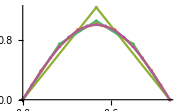

```mathematica
Show[%439,ImageSize->Small]
```

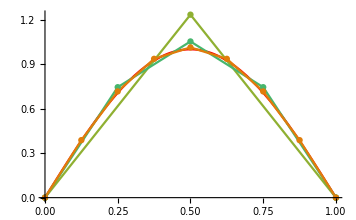

```mathematica
Show[H2,Table[ListPlot[Insert[Insert[Table[{k*1/(n),U[[Log[2,n],k]]},{k,1,n-1}],{0,0},1],{1,0},n+1],Joined->True,PlotStyle->ColorData[97,n^2-1]],{n,{2,4,8}}],Table[ListPlot[Insert[Insert[Table[{k*1/(n),U[[Log[2,n],k]]},{k,1,n-1}],{0,0},1],{1,0},n+1],PlotStyle->ColorData[97,n^2-1]],{n,{2,4,8}}],Epilog->Inset[Framed[Column[{PointLegend[{ColorData[97,2^2-1],ColorData[97,4^2-1],ColorData[97,8^2-1]},{"2","4","8"}],LineLegend[{ColorData[97,1^2-1]},{"f(x)=Sin(πx)"}]}],RoundingRadius->2],Scaled[{0.8,0.85}]],PlotRange->Automatic]
```

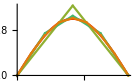

```mathematica
Show[H2,Table[ListPlot[Insert[Insert[Table[{k*1/(n),U[[Log[2,n],k]]},{k,1,n-1}],{0,0},1],{1,0},n+1],Joined->True,PlotStyle->ColorData[97,n^2-1]],{n,{2,4,8}}],Table[ListPlot[Insert[Insert[Table[{k*1/(n),U[[Log[2,n],k]]},{k,1,n-1}],{0,0},1],{1,0},n+1],PlotStyle->ColorData[97,n^2-1]],{n,{2,4,8}}],Epilog->Inset[Column[{PointLegend[{ColorData[97,2^2-1],ColorData[97,4^2-1],ColorData[97,8^2-1]},{"2","4","8"}],LineLegend[{ColorData[97,1^2-1]},{"f(x)=Sin(πx)"}]}],Scaled[{0.8,0.8}]],PlotRange->Automatic]
```

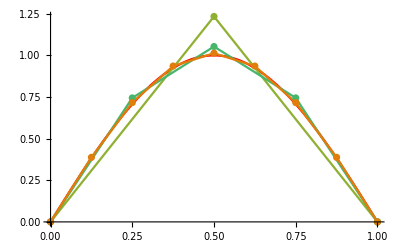

```mathematica
Show[%453,ImageSize->Tiny]
```

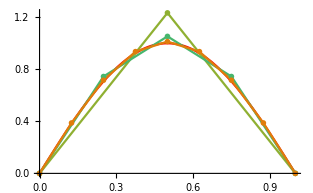

```mathematica
Show[H2,Table[ListPlot[Insert[Insert[Table[{k*1/(n),U[[Log[2,n],k]]},{k,1,n-1}],{0,0},1],{1,0},n+1],Joined->True,PlotStyle->ColorData[97,n^2-1]],{n,{2,4,8}}],Table[ListPlot[Insert[Insert[Table[{k*1/(n),U[[Log[2,n],k]]},{k,1,n-1}],{0,0},1],{1,0},n+1],PlotStyle->ColorData[97,n^2-1]],{n,{2,4,8}}],PlotRange->Automatic]
```

```mathematica
Show[%455,ImageSize->{8,5},AspectRatio->Full]
```

-Graphics-

```mathematica
Show[%455,ImageSize->Tiny]
```

-Graphics-

```mathematica
Show[%456,PlotLabel->None,LabelStyle->{2,GrayLevel[0]}]
```

-Graphics-

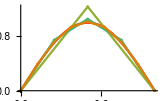

```mathematica
Show[%458,PlotLabel->None,LabelStyle->{4,GrayLevel[0]}]
```